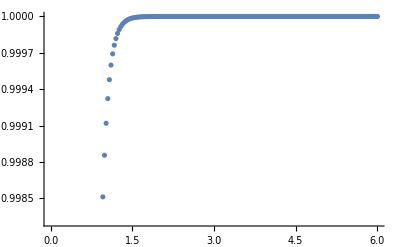

```mathematica
explicitEuler[n_]  := (
h = 6/n;
y = Table[0,{n+1}];
y[[1]] = 0.1;
For[i=1,i<n+1,i++,
	y[[i+1]]= y[[i]]+h*10*y[[i]]*(1-y[[i]]);
];
ListPlot[Table[{i*h,y[[i]]},{i,0,n}]]
)


implicitEuler[n_]:=(
h = 6/n;
y = Table[0,{n+1}];
y[[1]] = 0.1;
For[i = 1,i<n+1,i++,
	initialGuess =y[[i]]+10.*h*y[[i]](1-y[[i]]);
	y[[i+1]]=yNew/.FindRoot[yNew==y[[i]]+h*10.*yNew*(1-yNew),{yNew,initialGuess}]
];
ListPlot[Table[{i*h,y[[i]]},{i,0,n}]]
)

implicitEuler[200]
```